# Ray Tracing Kerr

## Equations of Motion

To begin we need to set up the equations of motion. We will take the equations for a null geodesic in the Hamiltonian formulation ref: . No specific additional inputs are provided beyond the metric - in analytic form - and the form of the Hamiltonian governing geodesic motion. 

Define the components of the metric

```mathematica
ρ2 = (r[λ]^2+a^2*Cos[θ[λ]]^2);
Δ = (r[λ]^2 -2*r[λ] + a^2);
B=(r[λ]^2+a^2)^2−a^2*Δ*Sin[θ[λ]]^2;
```

Take various derivatives of the metric components

```mathematica
x1= D[Δ/(2*ρ2),r[λ]];
x2 = D[Δ/(2*ρ2),θ[λ]];
x3= D[1/(2*ρ2),r[λ]];
x4 = D[1/(2*ρ2),θ[λ]];
x5 = D[(ρ2 - 2*r[λ])/(2*Δ*ρ2*Sin[θ[λ]]^2),r[λ]];
x6= D[(ρ2 - 2*r[λ])/(2*Δ*ρ2*Sin[θ[λ]]^2),θ[λ]];
x7 = D[B/(2*Δ*ρ2),r[λ]];
x8 = D[B/(2*Δ*ρ2),θ[λ]];
x9 = D[(2*a*r[λ])/(Δ*ρ2),r[λ]];
x10 = D[(2*a*r[λ])/(Δ*ρ2),θ[λ]];
```

With the components of the metric so defined - here specialising to the case of Kerr - we get the following equations of motion for {X^m, P_m,}. 

Note that, since in the case of Kerr, and in general for a stationary 4d spacetime we don’t need to evolve the P_t, P_phi components of the momentum. 

Note further that the energy E = -P_t = 1 of the photon has been scaled out of the equations; All the momenta are correspondingly scaled by a factor of 1/E.

```mathematica
eom = {
r'[λ]==(Δ/ρ2)*pr[λ],
θ'[λ]==ρ2^(-1)*pθ[λ],
ϕ'[λ]==((ρ2 - 2*r[λ])*L + 2*a*r[λ]*Sin[θ[λ]]^2)/(Δ*ρ2*Sin[θ[λ]]^2),
t'[λ]== 1+ (2*r[λ]*(r[λ]^2+a^2) - 2*r[λ]*a*L)/(Δ*ρ2),
pr'[λ] == (-x1*pr[λ]^2 - x3*pθ[λ]^2 - x5*L^2 + x7 - x9*L),
pθ'[λ] == (-x2*pr[λ]^2 - x4*pθ[λ]^2 -x6*L^2 +x8 - x10*L)
};
```

Can we use a rule to impose P^2 = 0 as a way to simplify the above expressions? Looks tricky

```mathematica
(*rule1 = {pr[λ]^2  -> -pθ[λ]^2*(1/Δ) - L^2*(ρ2 - 2*r[λ])/(Δ*Sin[θ[λ]])^2 - 4*L*a*r/(Δ)^2 + B/(Δ)^2}; )*
```

We will be evolving the geodesics backwards from the position of an observer. It is useful to define the following ‘reversed’ set of equations of motion to adapt to that setup.

```mathematica
eomback = {
r'[λ]==-(Δ/ρ2)*pr[λ],
θ'[λ]==-ρ2^(-1)*pθ[λ],
ϕ'[λ]==-((ρ2 - 2*r[λ])*L + 2*a*r[λ]*Sin[θ[λ]]^2)/(Δ*ρ2*Sin[θ[λ]]^2),
t'[λ]==-( 1+ (2*r[λ]*(r[λ]^2+a^2) - 2*r[λ]*a*L)/(Δ*ρ2)),
pr'[λ] ==- (-x1*pr[λ]^2 - x3*pθ[λ]^2 - x5*L^2 + x7 - x9*L),
pθ'[λ] ==- (-x2*pr[λ]^2 - x4*pθ[λ]^2 -x6*L^2 +x8 - x10*L)
};
```

## Initial Conditions

After defining the appropriate equations of motion we’ll need to take some care in specifying the initial conditions for the geodesics we’re shooting from the position of the observer. 

Take units in which the black hole mass is M=1. The we specify the background by fixing the black hole spin aI ϵ [0,1].

```mathematica
aI = 1;
```

```mathematica
horizonRadius = 1 +Sqrt[ 1 - aI^2];
```

The geodesics are started at position (r,θ,ϕ,t) = (rI, θI, 0, 0) and evolved forward in affine parameter time λ ϵ [0,λF].

```mathematica
λF = 1000;
```

With the initial position set, we need to also specify the four components of the initial momentum. One is the energy and this has been set to E=1. 

For the remaining components (P_r,P_θ, P_ϕ) we will use a parameterization in terms of celestial coordinates (x,y) on the observer’s sky; x, is the ‘azimuthal’ angle and y the ‘polar’ angle in the observers frame such that the incident null geodesic appears to arrive from direction (x,y). (see attached notes).

This initial direction corresponds to the tangent to the null geodesic at the observers position, hence its velocity at that point, or, via the metric, its momentum. 

Note finally that the relations between (x,y) and (P_r,P_θ, P_ϕ) given here are valid in the limit rI >>r_s. 

The initial angular momentum of the photon is given by

```mathematica
LI =( Sin[θI]^2/((rI^2+aI^2*Cos[θI]^2) - 2*rI))*((rI^2+aI^2*Cos[θI]^2)*(rI^2 -2*rI + aI^2)*Sin[y]*Cos[x]*1/(rI*Sin[θI]) + 2*aI*rI)
```

Then the set of initial conditions we need to provide for the equations of motion ‘eomback’ are

```mathematica
initialConditions =
{
r[0]    ==  rI,
θ[0]   == θI,
ϕ[0]    == 0,
t[0] == 0,
pr[0] == -((rI^2+aI^2*Cos[θI]^2)/(rI^2 -2*rI + aI^2))*Cos[y],
pθ[0] == ((rI^2+aI^2*Cos[θI]^2)/rI)*Sin[y]*Sin[x]
}
```

Take care with whether the geodesic is ‘incoming’ or ‘outgoing’ at the observers position. This flips the sign on the momenta above.

## Manipulate geodesic plot

In this section we use the equations of motion and the initial conditions set above and scan over a range of control parameters ( aI, λF, rI, θI, x, y ) to follow/plot the motion of the geodesics in space. 

Note the use of the ‘EventLocator’ option in NDSolve; this is used to track whether the geodesic is about to cross the horizon - the threshold for this can be set closer than 1.1*horizonRadius, it’s current value.

```mathematica
Manipulate[LI=( Sin[θI]^2/((rI^2+aI^2*Cos[θI]^2) - 2*rI))*((rI^2+aI^2*Cos[θI]^2)*(rI^2 -2*rI + aI^2)*Sin[y]*Cos[x]*1/(rI*Sin[θI]) + 2*aI*rI);
horizonRadius = 1 +Sqrt[ 1 - aI^2];
initialConditions =
{
r[0]    ==  rI,
θ[0]   == θI,
ϕ[0]    == 0,
t[0] == 0,
pr[0] == -((rI^2+aI^2*Cos[θI]^2)/(rI^2 -2*rI + aI^2))*Cos[y],
pθ[0] == ((rI^2+aI^2*Cos[θI]^2)/rI)*Sin[y]*Sin[x]
};

Quiet[
eomSoln=
NDSolve[
        {eom,initialConditions}/.{L-> LI,a-> aI},
        {r,θ,ϕ,t,pr,pθ},
        {λ,0,λF},
   Method->{"EventLocator", "Event"->(r[λ]- 1.1*horizonRadius ),"EventAction":> Throw[λF =λ,"StopIntegration"]}

        ];
     ];
rF = r[λF]/.eomSoln[[1]];
frame = If[rF > rI,
rF,
rI];
ParametricPlot3D[
                { 
           r[λ]*Sin[θ[λ]]*Cos[ϕ[λ]],
                 r[λ]*Sin[θ[λ]]*Sin[ϕ[λ]],
                 r[λ]*Cos[θ[λ]]
                }/.eomSoln,
                 {λ,0,λF},
                  PlotRange->
                           {
                            {-frame,frame},
                            {-frame,frame},
                            {-frame,frame}
                          },
                  PerformanceGoal->"Speed",
                  PlotPoints ->200,
                  MaxRecursion->8,(*
               ViewPoint->rightViewPoint,*)
                  SphericalRegion->True,
              Mesh -> 4,
              Ticks-> Automatic
               ],{λF,0.1,3000}, {rI,5,10}, {θI ,0.1,Pi-0.1},{aI,0.5,1},{x,0,2},{y,0,2}]
```

## Scan x,y

In this section we’re focussed on plotting the black hole shadow. It makes use of the equations of motion ‘eomback’ defined in the first section - so that needs to be initialised first before executing anything here. Otherwise the initial conditions are repeated as they’re scanned over locally in this section. 

First define an empty array XY; this will hold the (x,y) values of the geodesics with initial conditions that lead to horizon crossing.

```mathematica
XY ={};
```

Next set up the initial conditions we’ll be scanning over. This is as before, eg. geodesic plotting in the Manipulate section, except that we’re going to scan over x,y so they aren’t pre-specified.

```mathematica
{rI = 20, θI = Pi/2,aI = 1,λF=500};
```

The step size in the scan over x,y values as well as the range can be restricted. Note that x should go over the full range from 0 to 2π. However y need not range over such a large value - one expects the black hole to be centered at y = 0 and only extend in a small range around that. 

Perhaps some kind of root finding method to optimise finding the appropriate range for a general solution? Else guestimate.

```mathematica
For[y=0,y<Pi,y+=0.01,
For[x=0,x<2*Pi,x+=0.01,

LI=( Sin[θI]^2/((rI^2+aI^2*Cos[θI]^2) - 2*rI))*(-(rI^2+aI^2*Cos[θI]^2)*(rI^2 -2*rI + aI^2)*Sin[y]*Cos[x]*1/(rI*Sin[θI]) + 2*aI*rI);
		
horizonRadius = 1 +Sqrt[ 1 - aI^2];
		
initialConditions =
{
r[0]    ==  rI,
θ[0]   == θI,
ϕ[0]    == 0,
t[0] == 0,
pr[0] == ((rI^2+aI^2*Cos[θI]^2)/(rI^2 -2*rI + aI^2))*Cos[y],
pθ[0] == -((rI^2+aI^2*Cos[θI]^2)/rI)*Sin[y]*Sin[x]
};

	Quiet[
	eomSoln=
	NDSolve[
        {eomback,initialConditions}/.{L-> LI,a-> aI},
        {r,θ,ϕ,t,pr,pθ},
        {λ,0,λF},
   Method->{"EventLocator", "Event"->(r[λ]- 1.1*horizonRadius ),"EventAction":> Throw[{XY= Append[XY,{Sin[y]Cos[x],Sin[y]Sin[x]}]},"StopIntegration"]}
                         ];
                    ];
];
];
```

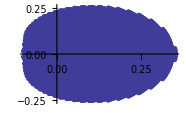

```mathematica
ListPlot[XY]
```

```mathematica
(*Better timing, number of points, by restricting y to a smaller domain*)
```

## Generate full image

```mathematica
phi = {};
theta={};
```

```mathematica
{rI = 40, θI = Pi/2,aI = 0,λF=500};
```

```mathematica
For[y=0,y<Pi,y+=0.1,
For[x=0,x<2*Pi,x+=0.1,
λbh = Infinity;
LI=( Sin[θI]^2/((rI^2+aI^2*Cos[θI]^2) - 2*rI))*(-(rI^2+aI^2*Cos[θI]^2)*(rI^2 -2*rI + aI^2)*Sin[y]*Cos[x]*1/(rI*Sin[θI]) + 2*aI*rI);
		
horizonRadius = 1 +Sqrt[ 1 - aI^2];
		
initialConditions =
{
r[0]    ==  rI,
θ[0]   == θI,
ϕ[0]    == 0,
t[0] == 0,
pr[0] == ((rI^2+aI^2*Cos[θI]^2)/(rI^2 -2*rI + aI^2))*Cos[y],
pθ[0] == -((rI^2+aI^2*Cos[θI]^2)/rI)*Sin[y]*Sin[x]
};

	Quiet[
	eomSoln=
	NDSolve[
        {eomback,initialConditions}/.{L-> LI,a-> aI},
        {r,θ,ϕ,t,pr,pθ},
        {λ,0,λF},
   Method->{"EventLocator", "Event"->(r[λ]- 1.1*horizonRadius ),"EventAction":> Throw[{λbh = λ},"StopIntegration"]}
                         ];
                    ];
If[λbh > λF,
{theta = Append[theta,{{x,y},θ[λF]/.eomSoln[[1]]}],
phi = Append[phi,{{x,y},ϕ[λF]/.eomSoln[[1]]}]};,
{theta = Append[theta,{{x,y},0}],
phi = Append[phi,{{x,y},0}]};
];
];
];
```

```mathematica
fphi = Interpolation[phi]
```

InterpolatingFunction[{{0.,6.2},{0.,3.1}},<>]

```mathematica
ftheta = Interpolation[theta]
```

InterpolatingFunction[{{0.,6.2},{0.,3.1}},<>]

```mathematica
Plot3D[ftheta,{x,0,2*Pi},{y,0,Pi}]
```

-Graphics3D-

```mathematica
Ff[{x_,y_}]:= {fphi,ftheta}
```

```mathematica
ImageTransformation[-Graphics-,fphi]
```

-Graphics-

## Testbed

```mathematica
?ListInterpolation
```

ListInterpolation[array] constructs an InterpolatingFunction object that represents an approximate function that interpolates the array of values given. 
ListInterpolation[array,{{x_min,x_max},{y_min,y_max},…}] specifies the domain of the grid from which the values in array are assumed to come.

```mathematica
?ImageTransformation
```

ImageTransformation[image,function] gives an image in which each pixel at position {x,y} corresponds to the position function[{x,y}] in image.
ImageTransformation[image,function,size] gives an image of the specified size.

```mathematica
?Interpolation
```

Interpolation[{f_1,f_2,…}] constructs an interpolation of the function values f_i, assumed to correspond to x values 1, 2, … . 
Interpolation[{{x_1,f_1},{x_2,f_2},…}] constructs an interpolation of the function values f_i corresponding to x values x_i.
Interpolation[{{{x_1,y_1,…},f_1},{{x_2,y_2,…},f_2},…}] constructs an interpolation of multidimensional data.
Interpolation[{{{x_1,…},f_1,df_1,…},…}] constructs an interpolation that reproduces derivatives as well as function values.
Interpolation[data,x] find an interpolation of data at the point x.

```mathematica
?ImageTransformation
```

RowBox[{"ImageTransformation", "[", RowBox[{StyleBox["image", "TI"], ",", StyleBox["function", "TI"]}], "]"}] gives an image in which each pixel at position RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}] corresponds to the position RowBox[{StyleBox["function", "TI"], "[", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], "]"}] in StyleBox["image", "TI"].
RowBox[{"ImageTransformation", "[", RowBox[{StyleBox["image", "TI"], ",", StyleBox["function", "TI"], ",", StyleBox["size", "TI"]}], "]"}] gives an image of the specified size.